# LD view - factor between triangles, testing computation algorithms

Author : Martin Horvat, August 2016

## Subdivision

```mathematica
Clear[LoopSubdivision];
LoopSubdivision[{v1_,v2_,v3_}]:=
{
{v1,(v1+v2)/2,(v1+v3)/2},
{(v1+v2)/2,v2,(v2+v3)/2},
{(v1+v3)/2,(v2+v3)/2,v3},
{(v1+v2)/2,(v2+v3)/2,(v1+v3)/2}
};

Clear[Subdivision];
Subdivision[T_List,n_]:=If[Depth[T]==2,Subdivision[{T},n],Nest[Flatten[Map[LoopSubdivision,#],1]&,T,n]];
```

## View factor calculation

```mathematica
Clear[R];
R[T_List,a_,b_]:=T[[1]]+(T[[2]]-T[[1]])*a+(T[[3]]-T[[1]])*b;

Clear[LDViewFactor];
LDViewFactor[T_,f_]:=Module[{n,A,a,b,a1,a2,b1,b2,F},

n=Table[Cross[T[[i,2]]-T[[i,1]],T[[i,3]]-T[[i,1]]],{i,2}];
A=Norm/@n;
n=n/A;
A/=2;

F[a1_,b1_,a2_,b2_,{i1_,i2_}]:=Module[{v,t,c1,c2},
v=R[T[[i2]],a2,b2]-R[T[[i1]],a1,b1];
t=Norm[v];
v/=t;
{c1,c2}={n[[i1]].v,-n[[i2]].v};
c1*c2*f[c1]/t^2
];

4*A*NIntegrate[
{F[a1,b1,a2,b2,{1,2}],F[a1,b1,a2,b2,{2,1}]},
{a1,0,1},{b1,0,1-a1},
{a2,0,1},{b2,0,1-a2}
](*F_{1->2},F_{2->1}*)
];


Clear[LDViewFactorSimplified];
LDViewFactorSimplified[T_,f_]:=Module[{n,A,r,F},

n=Table[Cross[T[[i,2]]-T[[i,1]],T[[i,3]]-T[[i,1]]],{i,2}];
A=Norm/@n;
n=n/A;
A/=2;
r=(#[[1]]+#[[2]]+#[[3]])/3&/@T;

F[{r1_,r2_},{n1_,n2_}]:=Module[{v,t,c1,c2},
v=r2-r1;
t=Norm[v];
v/=t;
{c1,c2}={n1.v,-n2.v};
c1*c2*f[c1]/t^2
];

A*{F[r,n],F[Reverse[r],Reverse[n]]} (*F_{1->2},F_{2->1}*)
];

Clear[LDViewFactorSubdivision];
LDViewFactorSubdivision[T_,f_,ns_]:=Module[{n,n1,A,F,T1,A1,C1,i},
(* Data of the two triagles *)
n=Table[Cross[T[[i,2]]-T[[i,1]],T[[i,3]]-T[[i,1]]],{i,2}];
A=Norm/@n;
n=n/A;
A/=2;

T1=Table[Subdivision[{T[[i]]},ns],{i,2}];
C1=Table[Map[(#[[1]]+#[[2]]+#[[3]])/3&,T1[[i]]],{i,2}];
A1=Table[Map[Norm[Cross[#[[2]]-#[[1]],#[[3]]-#[[1]]]]&,T1[[i]]],{i,2}]/2;

(* F(r[[1]] -> r[[2]]) *)
F[{r1_,r2_},{n1_,n2_}]:=Module[{v,t,c1,c2},
v=r2-r1;
t=Norm[v];
{c1,c2}={n1.v,-n2.v}/t;
c1*c2*f[c1]/t^2
];

n1=Reverse[n];
{
Sum[A1[[1,i]]A1[[2,j]]F[{C1[[1,i]],C1[[2,j]]},n],{i,Length[C1[[1]]]},{j,Length[C1[[2]]]}],
Sum[A1[[2,i]]A1[[1,j]]F[{C1[[2,i]],C1[[1,j]]},n1],{i,Length[C1[[2]]]},{j,Length[C1[[1]]]}]
}/Reverse[A]
];
```

## Testing

```mathematica
s=0.5;
T1=s{{0,0,0},{1,0,0},{1/2,1,0}};
T2={1,1,1}+Map[EulerMatrix[{0,(5 π)/4,0}].#&,T1];
```

```mathematica
Graphics3D[{Triangle[T1],Triangle[T2]},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
resExact=LDViewFactor[{T1,T2},1#&]/s^2
```

{0.0719691,0.075628}

```mathematica
LDViewFactorSimplified[{T1,T2},1.#&]/s^2
```

{0.0706482,0.07429}

```mathematica
res1=Table[{n,LDViewFactorSubdivision[{T1,T2},1.#&,n]/s^2},{n,0,5}];
```

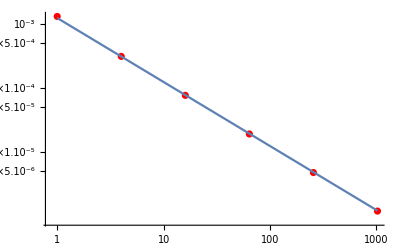

```mathematica
Show[
ListLogLogPlot[Table[{4^r[[1]],(resExact-r[[2]])[[1]]},{r,res1}],PlotRange->All,PlotStyle->Red],
LogLogPlot[1.25*10^-3 x^-1,{x,1,1024}]
]
```

### Extrapolation scheme

```mathematica
sol=Solve[
{I0==Ioo+ a+b,
I1==Ioo+a 4^-1 + b 4^-2,
I2==Ioo+a 4^-2 + b 4^-4},
{Ioo,a,b}]
```

{{Ioo→1/45 (I0-20 I1+64 I2),a→-4/9 (I0-17 I1+16 I2),b→64/45 (I0-5 I1+4 I2)}}

```mathematica
(Ioo/.sol[[1]])/.{I0->res1[[1,2]],I1->res1[[2,2]],I2->res1[[3,2]]}
```

{0.0719692,0.0756279}